## Specification

### Event format

All events are associations with the keys “Type”, “Provenance”, and “Content”.

“Type” is a string.

“Content” is an association with a format corresponding to the “Type”.

“Provenance” has keys “TabletID” (from Oracc), “Line”, “Creator”, “Reviewed”, and “Notes”.

### Event types

#### RelativePosition

```mathematica
<|
"Source"->...,
"Target"->...,
"Displacement"->DiaryDisplacment[...],
"Direction"->DiaryDirection[...],
"Date"->DiaryDate[...]
|>
```

#### ZodiacalPosition

```mathematica
<|
"Object"->,
"Sign"->,
"Direction"->DiaryDirection[...],
"Date"->DiaryDate[...]
|>
```

#### WindDirection

```mathematica
<|
"Direction"->"North"|"South"|"East"|"West",
"Date"->DiaryDate[...]
|>
```

#### Weather

```mathematica
<|
"Tags"->{...},
"Date"->DiaryDate[...]
|>
```

#### AstronomicalNote

```mathematica
<|
"Content"->String,
"Date"->DiaryDate[...]
|>
```

#### HistoricalNote

```mathematica
<|
"Content"->String,
"Date"->DiaryDate[...]
|>
```

### Helper types

#### DiaryDate

Used to represent dates in the Babylonian calendar. Partial Julian and Babylonian dates are also supported.

```mathematica
DiaryDate[<|
"JulianYear"->(*Year AD*),
"JulianMonth"->,
"JulianDay"->,
"BabylonianYear"->{(*Regnal year*),(*King*)},
"BabylonianMonth"->(*Babylonian month number*),
"BabylonianDay"->(*Babylonian day number*),
"Time"->"BeginningOfTheNight"|"FirstPartOfTheNight"|"MiddlePartOfTheNight"|"LastPartOfTheNight"|"Morning"|"Noon"|"Afternoon"|"Sunset"
|>]
```

Kings written as:

```mathematica
"AlexanderIII"|"AlexanderIV"|"ArtaxerxesI"|"ArtaxerxesII"|"ArtaxerxesIII"|"DariusII"|"DariusIII"|"NebukadnezarII"|"PhilipArrhidaeus"|"SeleucidEra"
```

DateObject can be used to convert to and from Babylonian dates:

```mathematica
DateObject[DiaryDate[...]]
```

```mathematica
DiaryDate[DateObject[...]]
```

#### DiaryDistance

```mathematica
DiaryDistance[<|
"Cubits"->Rational|_Missing,
"Fingers"->Rational|_Missing,
|>]
```

#### DiaryDisplacment [INCOMPLETE]

Used to represent displacements between objects in the sky.

```mathematica
DiaryDisplacment[<|
"Distance"->DiaryDistance[...],
"Relation"->"Above"|"Below"|"InFrontOf"|"Behind"
|>]
```

#### DiaryDirection [INCOMPLETE]

Used to represent a direction toward an observation in the sky.

```mathematica
DiaryDirection[<|
"Distance"->DiaryDistance[...],
"Direction"->"West"|"North"|"South"|"East"(*NORTH SOUTH EAST WEST?*)
|>]
```

## Implementation

```mathematica
Cases[DeleteMissing[Lookup[#,{"obj1","obj2"}]&/@allEvents,1,2],{_,"moon"}]
```

{{mars,moon}}

```mathematica
GroupBy[allEvents,Lookup[{"j","month","day"}]][{-103,2,26}]
```

{<|j→-103,m→5,rel2→low_to_the_south,kusd20→1.,balanced→Null,kus→1,obj2→venus,kus2d24→2.,id→5447,kusp2→kus,day→26,number→5447,kus2→2,shift→shift,event-type→configuration,king→seleucid_era,obj1→moon,mjd→-716426,kusfrac2→Null,kusfrac→Null,kus2d20→2.,kusd24→1.,time→last_part_of_night,kusp→kus,type_filter_key→configuration,si2→Null,lfdnr→9,torel→Null,month→2,rel→in_front_of,year_filter_key→208,table→pl103A,si→Null,sip→Null,sip2→Null,t→18,type→event,year→208|>,<|j→-103,m→5,rel2→Null,kusd20→Null,balanced→Null,kus→Null,obj2→taurus,kus2d24→Null,id→5448,kusp2→Null,day→26,number→5448,kus2→Null,shift→Null,event-type→configuration,king→seleucid_era,obj1→mercury,mjd→-716426,kusfrac2→Null,kusfrac→Null,kus2d20→Null,kusd24→Null,time→last_part_of_night,kusp→Null,type_filter_key→configuration,si2→Null,lfdnr→10,torel→Null,month→2,rel→is_standing_in,year_filter_key→208,table→pl103A,si→Null,sip→Null,sip2→Null,t→18,type→event,year→208|>,<|j→-103,m→5,rel2→Null,kusd20→Null,balanced→Null,kus→Null,obj2→gemini,kus2d24→Null,id→5449,kusp2→Null,day→26,number→5449,kus2→Null,shift→Null,event-type→configuration,king→seleucid_era,obj1→mercury,mjd→-716426,kusfrac2→Null,kusfrac→Null,kus2d20→Null,kusd24→Null,time→last_part_of_night,kusp→Null,type_filter_key→configuration,si2→Null,lfdnr→11,torel→Null,month→2,rel→is_standing_in,year_filter_key→208,table→pl103A,si→Null,sip→Null,sip2→Null,t→18,type→event,year→208|>}

```mathematica
gs=Graph[#,VertexLabels->"Name"]&/@Apply[UndirectedEdge,Map[Lookup[{"obj1","obj2"}],GroupBy[allEvents,Lookup[{"j","month","day"}]],{2}],{2}];
```

```mathematica
Max[VertexCount/@gs]
```

28

```mathematica
Position[tabletEvents,<|"j"->-157,"m"->8,"rel2"->Null,"kusd20"->1.,"balanced"->Null,"kus"->1,"obj2"->"jupiter","kus2d24"->Null,"id"->3584,"kusp2"->Null,"day"->25,"number"->3584,"kus2"->Null,"shift"->Null,"event-type"->"configuration","king"->"seleucid_era","obj1"->"moon","mjd"->-736065,"kusfrac2"->Null,"kusfrac"->Null,"kus2d20"->Null,"kusd24"->1.,"time"->"last_part_of_night","kusp"->"kus","type_filter_key"->"configuration","si2"->Null,"lfdnr"->16,"torel"->"to_the_west","month"->4,"rel"->"in_front_of","year_filter_key"->154,"table"->"pl157A","si"->Null,"sip"->Null,"sip2"->Null,"t"->11,"type"->"event","year"->154|>,{2}]
```

{{102,Key[event-3584]}}

```mathematica
rawJSON[[43]]
```

```mathematica
rawJSON[[102]]
```

These just look wrong:

```mathematica
GroupBy[allEvents,Lookup[{"j","month","day"}]][{-157,4,25}]
```

{<|j→-157,m→8,rel2→Null,kusd20→1.,balanced→Null,kus→1,obj2→jupiter,kus2d24→Null,id→3584,kusp2→Null,day→25,number→3584,kus2→Null,shift→Null,event-type→configuration,king→seleucid_era,obj1→moon,mjd→-736065,kusfrac2→Null,kusfrac→Null,kus2d20→Null,kusd24→1.,time→last_part_of_night,kusp→kus,type_filter_key→configuration,si2→Null,lfdnr→16,torel→to_the_west,month→4,rel→in_front_of,year_filter_key→154,table→pl157A,si→Null,sip→Null,sip2→Null,t→11,type→event,year→154|>,<|j→-157,m→8,rel2→Null,kusd20→Null,balanced→Null,kus→Null,obj2→cancer,kus2d24→Null,id→3585,kusp2→Null,day→25,number→3585,kus2→Null,shift→Null,event-type→configuration,king→seleucid_era,obj1→jupiter,mjd→-736065,kusfrac2→Null,kusfrac→Null,kus2d20→Null,kusd24→Null,time→beginning_of_night,kusp→Null,type_filter_key→configuration,si2→Null,lfdnr→17,torel→Null,month→4,rel→is_standing_in,year_filter_key→154,table→pl157A,si→Null,sip→Null,sip2→Null,t→11,type→event,year→154|>,<|j→-157,m→8,rel2→Null,kusd20→Null,balanced→Null,kus→Null,obj2→cancer,kus2d24→Null,id→3586,kusp2→Null,day→25,number→3586,kus2→Null,shift→Null,event-type→configuration,king→seleucid_era,obj1→venus,mjd→-736065,kusfrac2→Null,kusfrac→Null,kus2d20→Null,kusd24→Null,time→beginning_of_night,kusp→Null,type_filter_key→configuration,si2→Null,lfdnr→18,torel→Null,month→4,rel→is_standing_in,year_filter_key→154,table→pl157A,si→Null,sip→Null,sip2→Null,t→11,type→event,year→154|>,<|j→-157,m→8,rel2→Null,kusd20→Null,balanced→Null,kus→Null,obj2→cancer,kus2d24→Null,id→3587,kusp2→Null,day→25,number→3587,kus2→Null,shift→Null,event-type→configuration,king→seleucid_era,obj1→mercury,mjd→-736065,kusfrac2→Null,kusfrac→Null,kus2d20→Null,kusd24→Null,time→beginning_of_night,kusp→Null,type_filter_key→configuration,si2→Null,lfdnr→19,torel→Null,month→4,rel→is_standing_in,year_filter_key→154,table→pl157A,si→Null,sip→Null,sip2→Null,t→11,type→event,year→154|>}

```mathematica
Values[KeySelect[rawJSON[[102]],StringMatchQ["event-*"]]][[All,"month"]]
```

{4,4,4,4,4,4,4,4,4,4,4,4,4,4}

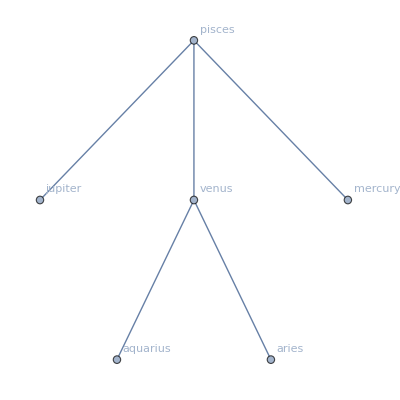
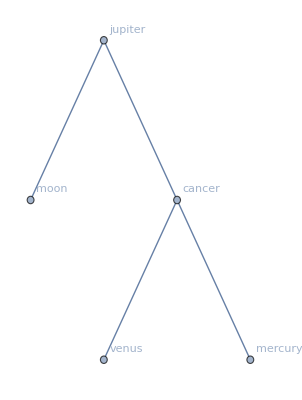
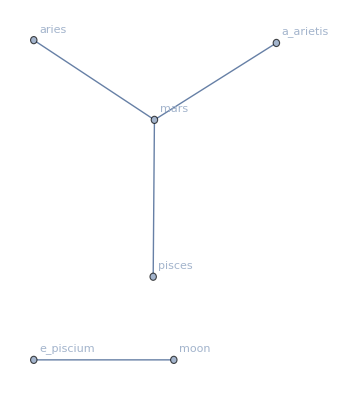
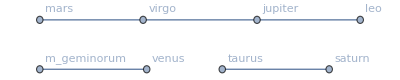
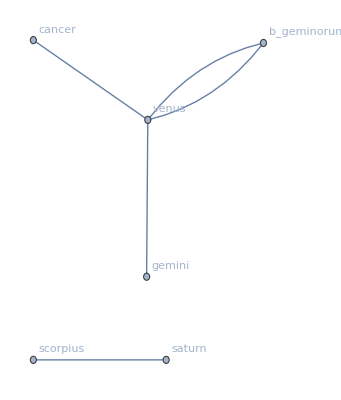
<|{-125,13,27}→-Graphics-,{-157,4,25}→-Graphics-,{-105,1,24}→-Graphics-,{-119,3,29}→-Graphics-,{-105,1,27}→-Graphics-|>

```mathematica
TakeLargestBy[KeySelect[gs,FreeQ[Null]],Max[VertexCount/@ConnectedGraphComponents[#]]&,5]
```

```mathematica
Union@DeleteMissing[Lookup[#,{"obj1","obj2"}]&/@allEvents,1,2][[All,2]]
```

{a_arietis,a_geminorum,a_leonis,a_librae,aquarius,aries,a_scorpii,a_tauri,a_virginis,b_arietis,b_capricorni,b_geminorum,b_librae,b_scorpii,b_tauri,b_virginis,cancer,capricorn,d_cancri,d_capricorni,d_scorpii,e_cancri,e_geminorum,electra,e_piscium,eps_leonis,g_cancri,g_capricorni,gemini,g_geminorum,g_virginis,jupiter,leo,libra,mars,mercury,m_geminorum,moon,pisces,p_scorpii,r_leonis,sagittarius,saturn,scorpius,taurus,th_cancri,th_leonis,th_ophiuchi,venus,virgo,z_tauri}

```mathematica
Select[allEvents,!MissingQ[#obj1]&&!MissingQ[#obj2]&]
```

{<|j→-103,m→4,rel2→low_to_the_south,kusd20→1.5,balanced→Null,kus→1,obj2→th_leonis,kus2d24→4.5,id→5442,kusp2→kus,day→8,16,torel→Null,month→2,rel→behind,year_filter_key→208,table→pl103A,si→Null,sip→Null,sip2→Null,t→30,type→event,year→208|>,4362}
 |  |  |  |

### Normal stars

```mathematica
normalStars=<|"EtaPiscium"->Entity["Star","EtaPiscium"],"BetaArietis"->Entity["Star","Sheratan"],"AlphaArietis"->Entity["Star","Hamal"],"EtaTauri"->Entity["Star","Alcyone"],"AlphaTauri"->Entity["Star","Aldebaran"],"BetaTauri"->Entity["Star","Alnath"],"XiTauri"->Entity["Star","XiTauri"],"EtaGeminorum"->Entity["Star","Propus"],"MuGeminorum"->Entity["Star","Tejat"],"GammaGeminorum"->Entity["Star","Alhena"],"AlphaGeminorum"->Entity["Star","Castor"],"BetaGeminorum"->Entity["Star","Pollux"],"EtaCancri"->Entity["Star","EtaCancri"],"ThetaCancri"->Entity["Star","ThetaCancri"],"GammaCancri"->Entity["Star","AsellusBorealis"],"DeltaCancri"->Entity["Star","AsellusAustralis"],"EpsilonLeonis"->Entity["Star","EpsilonLeonis"],"AlphaLeonis"->Entity["Star","Regulus"],"RhoLeonis"->Entity["Star","RhoLeonis"],"ThetaLeonis"->Entity["Star","Chort"],"BetaVirginis"->Entity["Star","Alaraph"],"GammaVirginis"->Entity["Star","Porrima"],"AlphaVirginis"->Entity["Star","Spica"],"AlphaLibrae"->Entity["Star","Alpha1Librae"],"BetaLibrae"->Entity["Star","Zubeneshamali"],"DeltaScorpii"->Entity["Star","Dschubba"],"BetaScorpii"->Entity["Star","Beta2Scorpii"],"AlphaScorpii"->Entity["Star","Antares"],"ThetaOphiuchi"->Entity["Star","ThetaOphiuchi"],"BetaCapricorni"->Entity["Star","Dabih"],"GammaCapricorni"->Entity["Star","Nashira"],"DeltaCapricorni"->Entity["Star","DenebAlgiedi"]|>;
```

```mathematica
UnitConvert[EntityValue[Values@normalStars,"ProperMotion"]*Quantity[1000, "Years"],"Degrees"]
```

{0.00695 °,0.03923 °,0.06326 °,0.0129 °,0.05519 °,0.04873 °,0.0181 °,0.0163 °,0.03356 °,0.0186 °,0.06374 °,0.154 °,0.017 °,0.0223 °,0.02972 °,0.06362 °,0.012 °,0.06779 °,0.0018 °,0.0271 °,0.2191 °,0.1721 °,0.0146 °,0.03988 °,0.027 °,0.0105 °,0.00928 °,0.00692 °,0.00693 °,0.0136 °,0.05025 °,0.1082 °}

```mathematica
EntityValue[Values[normalStars],"RightAscension"]
```

{1 31,1 54,2 7,3 47,4 35,5 26,3 27,6 14,6 22,6 37,7 34,7 45,8 32,8 31,8 43,8 44,9 45,10 8,10 32,11 14,11 50,12 41,13 25,14 50,15 17,16 0,16 5,16 29,17 22,20 21,21 40,21 47}

```mathematica
UnitConvert[EntityValue[Values[normalStars],"ProperMotion"]*Quantity[500, "Years"],"Degrees"]
```

{0.00348 °,0.01961 °,0.03163 °,0.00647 °,0.0276 °,0.02436 °,0.00905 °,0.00815 °,0.01678 °,0.0093 °,0.03187 °,0.07698 °,0.0085 °,0.0112 °,0.01486 °,0.03181 °,0.00601 °,0.03389 °,0.00091 °,0.0136 °,0.1095 °,0.08603 °,0.00728 °,0.01994 °,0.0135 °,0.00524 °,0.00464 °,0.00346 °,0.00347 °,0.00679 °,0.02513 °,0.0541 °}

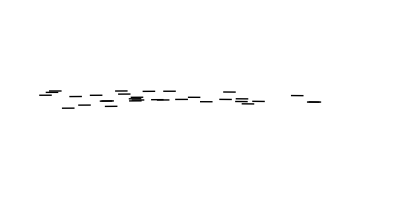

```mathematica
Graphics[Line[Map[Apply[{Mod[#2+15,360],#1}&],Values[Values/@normalStarPositions],{2}]],PlotRange->{{0,360},{-90,90}},PlotRangePadding->5,ImageSize->700]
```

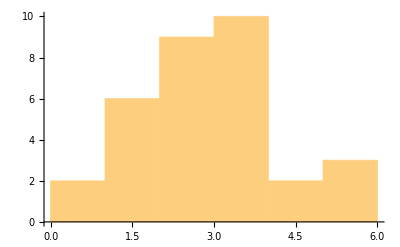

```mathematica
Histogram@EntityValue[Values[normalStars],"ApparentMagnitude"]
```

```mathematica
Max@EntityValue[Values[normalStars],"ApparentMagnitude"]
```

5.33

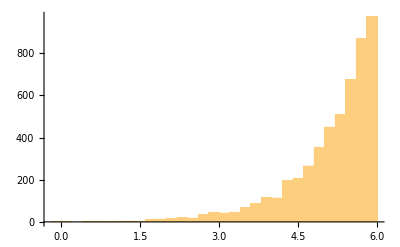

```mathematica
Histogram@EntityValue[EntityClass["Star","ApparentMagnitude"->LessThan[6]],"ApparentMagnitude"]
```

```mathematica
ListLinePlot[Map[Apply[{Mod[#2+15,360],#1}&],Values[Values/@normalStarPositions],{2}],PlotRange->{{0,360},All}]
```

```mathematica
Map[Apply[{Mod[#2+10,360],#1}&],Values[Values/@normalStarPositions],{2}]
```

{{{357.959,5.22948},{357.972,5.22952},{357.986,5.22956},{357.999,5.2296},994,{11.748,5.27372},{11.7629,5.27377},{11.778,5.27382}},30,{1}}
 |  |  |  |

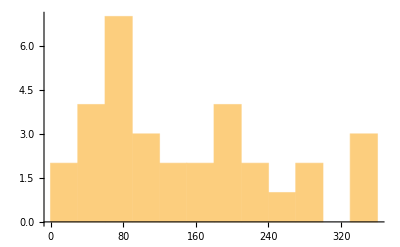

```mathematica
Histogram[normalStarPositions[[All,1,2]],{30}]
```

```mathematica
Manipulate[Graphics[Point[Reverse/@Values@normalStarPositions[[All,n]]],PlotRange->{{0,360},{-90,90}},PlotRangePadding->5,ImageSize->700],{n,1,1000,1}]
```

```mathematica
normalStarPositions=Import["~/Dropbox/brown/2019/asyrScience/finalProject/scripts/normalStarPositions/normalStarPositions.json","RawJSON"];
```

```mathematica
Subtract@@normalStarPositions[[11,{-1,1}]]
```

{0.0806312,13.78}

```mathematica
Apply[Subtract]@*Values/@normalStarPositions[[All,{1,2}]]
```

<|7097→{-0.0000391602,-0.0139229},8903→{-0.0000205121,-0.0139247},9884→{-9.54182×10^-6,-0.0139439},17702→{-0.0000934527,-0.0139254},21421→{-0.0000644817,-0.0139445},25428→{-0.0000819066,-0.0139286},16083→{-0.0000792238,-0.013956},29655→{-0.000132119,-0.0139113},30343→{-0.000106105,-0.0139455},31681→{-0.000117329,-0.0139288},36850→{-0.0000829389,-0.0138824},37826→{-0.0000874275,-0.013762},41909→{-0.000106086,-0.0139208},41822→{-0.000101494,-0.0139149},42806→{-0.000100422,-0.0139058},42911→{-0.0000549739,-0.0139405},47908→{-0.0000938934,-0.0139323},49669→{-0.0000611813,-0.0138635},51624→{-0.0000708093,-0.0139273},54879→{-0.0000309479,-0.0139429},57757→{-0.0000423809,-0.0141487},61941→{0.0000575435,-0.0137708},65474→{0.0000486149,-0.0139164},72603→{0.000108061,-0.0138984},74785→{0.000101674,-0.0139197},78401→{0.0001206,-0.0139258},78821→{0.000114834,-0.0139212},80763→{0.000126012,-0.0139218},84970→{0.00013665,-0.0139254},100345→{0.000122067,-0.0139375},106985→{0.000122367,-0.0139793},107556→{0.000198685,-0.0139733}|>

## Notes

Make UI?

Formalize weather tags

Market prices and river level

Include directions? (To the east, to the west, etc)

Add times to the BabylonianDate objects

What are the positions of the normal stars over time?

Summaries of positions at the end of each month

Eclipses

You could calculate the movement of the zodiac very easily

Deal with intercalation with BabylonianDate? How do you deal with VI_2?

Replace objects where all fields are missing?

Month lengths? -Graphics-(page about lunar 6)

Tag some observations with “I did not watch” (see page 21 of H&S)

“Passing by normal stars section”: -Graphics-

Same section^ show this: -Graphics-